## Rotational wave-function

```mathematica
phiM[phi_,M_]:=1/Sqrt[2π] Exp[ⅈ*M*phi*π/180];
```

```mathematica
MLIST[I3_]:=Table[i,{i,-I3,I3,1}];
MLIST[4]
```

{-4,-3,-2,-1,0,1,2,3,4}

#### Choose rotation/orientation angle (ϕ=20°)

```mathematica
ϕ=20;
```

### Rotational wave-function

```mathematica
Do[Print[m," -> | ",phiM[ϕ,m]," >"],{m,-4,4,1}]
```

-4 -> | ⅇ^(-(4 ⅈ π)/9)/(√(2 π)) >

-3 -> | ⅇ^(-(ⅈ π)/3)/(√(2 π)) >

-2 -> | ⅇ^(-(2 ⅈ π)/9)/(√(2 π)) >

-1 -> | ⅇ^(-(ⅈ π)/9)/(√(2 π)) >

0 -> | 1/(√(2 π)) >

1 -> | ⅇ^((ⅈ π)/9)/(√(2 π)) >

2 -> | ⅇ^((2 ⅈ π)/9)/(√(2 π)) >

3 -> | ⅇ^((ⅈ π)/3)/(√(2 π)) >

4 -> | ⅇ^((4 ⅈ π)/9)/(√(2 π)) >

### Rotational wave - function (real-part)

```mathematica
RephiM[phi_,M_]:=If[Im[phiM[phi,M]]==0,phiM[phi,M],Re[phiM[phi,M]]];
```

```mathematica
RephiM[20,4]
```

Sin[π/18]/(√(2 π))

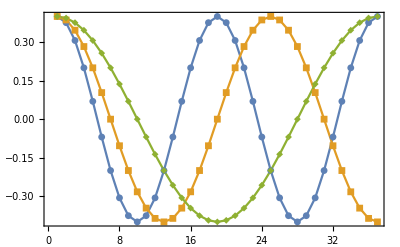

```mathematica
ListPlot[{Table[RephiM[phi,4],{phi,0,180,5}],Table[RephiM[phi,3],{phi,0,180,5}],Table[RephiM[phi,2],{phi,0,180,5}]},Joined->True,Axes->False,PlotMarkers->{Automatic, Small},Frame->True,PlotRange->All]
```

## Plot φ_M(ϕ)

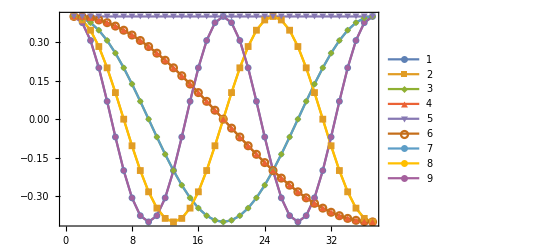

```mathematica
lp[I_]:=ListPlot[Table[Table[RephiM[phi,M],{phi,0,180,5}],{M,-I,I,1}],Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,PlotLegends->Automatic];
lp[4]
```

## Plot |Subscript[φ, M](ϕ)|^2